```mathematica
f[x_?OddQ]:=3x+1
f[x_?EvenQ]:=x/2
f1[x_?EvenQ]:=If[Mod[x-1,3]==0,{2x,(x-1)/3},2x]
```

```mathematica
f2[x_]:=f1[x]
f2[x_List]:=f1/@x
SetAttributes[f2,Listable]
```

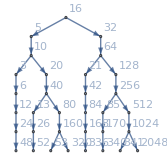

```mathematica
NestGraph[f1[#]&,16,7,VertexLabels->"Name"]
```

```mathematica
AdjacencyMatrix[%111]//ArrayPlot
```

-Graphics-

```mathematica
NestGraph[f1[#]&,1,20,
VertexLabels->"Name"]//UndirectedGraph//AdjacencyMatrix//ArrayPlot
```

-Graphics-

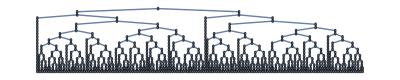

```mathematica
NestGraph[f1[#]&,16,20]//EdgeRules//TreePlot
```

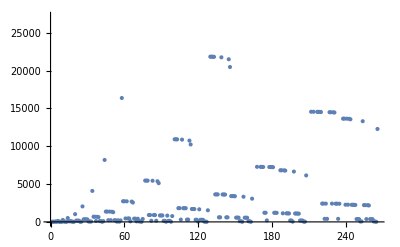

```mathematica
NestList[f2,16,15]//Flatten//ListPlot
```

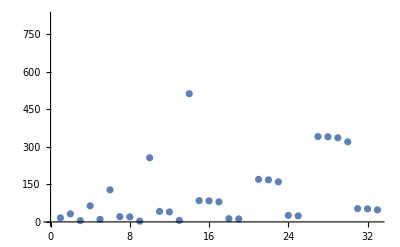

```mathematica
ListPlot[{16,32,5,64,10,128,21,20,3,256,42,40,6,512,85,84,80,13,12,1024,170,168,160,26,24,2048,341,340,336,320,53,52,48}]
```

1,2,4,8,1,16,2,32,5,4,64,10,8,1,128,21,20,3,16,2